```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},ColorFunction->"RustTones"]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤4],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},Mesh->All]
```

-Graphics3D-

```mathematica
Plot3D[1/(x^2+y^2),{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[x y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Im[ArcSin[(x+I y)^3]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Grid[Table[Plot3D[Sin[x y],{x,0,4},{y,0,4},PlotPoints->pp,MaxRecursion->mr,Mesh->None],{mr,{0,1,2}},{pp,{5,15}}]]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
{Plot3D[x^4-2 x^2+y^4-2 y^2+5,{x,-2,2},{y,-2,2}],Plot3D[x^4-2 x^2+y^4-2 y^2+1,{x,-2,2},{y,-2,2},PlotRange->{-2,2},ClippingStyle->None]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{Plot3D[1/(ChebyshevU[x y-1,2]),{x,-5,5},{y,-5,5}],Plot3D[1/(ChebyshevU[x y-1,2]),{x,-5,5},{y,-5,5},Exclusions->{x==0,y==0}]}
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},RegionFunction->Function[{x,y,z},0<x+y^2<Pi]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},6]]
```

-Graphics3D-

```mathematica
𝒟=MeshRegion[{{0,0},{5,-2},{3,0},{5,2}},Polygon[{1,2,3,4}]];
```

```mathematica
Plot3D[x^2+y^2,{x,y}∈𝒟]
```

-Graphics3D-

```mathematica
Graphics[𝒟]
```

-Graphics-

```mathematica
Graphics[Polygon[{1,2,3,4}]]
```

-Graphics-

```mathematica
Graphics3D[Polygon[{1,2,3,4}]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,20]]]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x],Cos[x]},{x,0,2 Pi},{y,0,2 Pi},PlotStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},AxesLabel->{x,y},PlotLabel->Sin[x y]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},6], ColorFunction->Function[{x,y,z}, Hue[z]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"SolarColors",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+Cos[y]],{x,y}∈Disk[{0,0},6], ColorFunction->Function[{x,y,z}, Hue[z]], PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x] Cos[y],{x,0,2 π},{y,0,2 π},PlotTheme->"Web"]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[1-x^2-y^2],{x,-1,1},{y,-1,1},Mesh->8,ColorFunction->Hue,MeshShading->{{Yellow,Orange},{Pink,Red}}]
```

-Graphics3D-

```mathematica
Plot3D[Tooltip[Sqrt[x y]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-2,2},{y,-2,2},RegionFunction->(#1^2+#2^2<4&),Filling->Bottom,FillingStyle->Directive[Opacity[0.4],Red]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[u v],{u,0,3},{v,0,3},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin [u v],{u,v}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
Plot3D[Sin [u v],{u,v}∈Disk[{0,0},3],ColorFunction->Hue,MeshShading->{{Yellow,Orange},{Pink,Red}}]
```

-Graphics3D-

```mathematica
Table[Plot3D[Sin [u v],{u,v}∈Disk[{0,0},i],ColorFunction->Hue,MeshShading->{{Yellow,Orange},{Pink,Red}}], {i, 1, 10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[Sin[x+y^2],{x,-2,2},{y,-2,2},Background->Black,Mesh->None,AxesStyle->White,Boxed->False]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2},BoundaryStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2},BoundaryStyle->Directive[Red,Thick]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2},BoundaryStyle->None]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2},BoundaryStyle->Thick,RegionFunction->Function[{x,y,z},x^2+y^2≥1]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,-2,2},{y,-2,2},BoundaryStyle->Thick,RegionFunction->Function[{x,y,z},x^2+y^2≤1]]
```

-Graphics3D-

```mathematica
Plot3D[Im[Sqrt[x+I y]],{x,-2,2},{y,-2,2},BoundaryStyle->Thick]
```

-Graphics3D-

```mathematica
{Plot3D[Sqrt[1-x^2-y^2],{x,0,1},{y,0,1}],Plot3D[Sqrt[1-x^2-y^2],{x,0,1},{y,0,1},BoxRatios->Automatic]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[y^2-x^2,{x,-4,4},{y,-4,4},MeshFunctions->{#3&},BoxRatios->{1,1,2}]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sin[x+I y]],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi}]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sin[x+I y]],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},ClippingStyle->None]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sin[x+I y]],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},ClippingStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sin[x+I y]],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},ClippingStyle->{Red,Blue}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},RGBColor[x,y,0.]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},RGBColor[x,y,z]]]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->(ColorData["DarkRainbow"][#3]&)]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->"DarkRainbow",PlotStyle->Directive[Opacity[0.5],Red]]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->Hue,MeshShading->{{Automatic,None},{None,Automatic}}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[Sin[x+I y]],{x,-2 Pi,2 Pi},{y,-2,2},ColorFunction->Function[{x,y,z},Hue@Rescale[Arg[Sin[x+I y]],{-Pi,Pi}]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[y,x,1]],ColorFunctionScaling->{True,False,False}]
```

-Graphics3D-

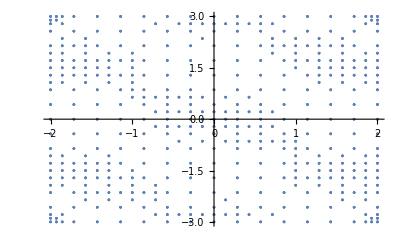

```mathematica
ListPlot[Reap[Plot3D[Sin[x] Sin[y],{x,-2,2},{y,-3,3},EvaluationMonitor:>Sow[{x,y}]]][[-1,1]]]
```

```mathematica
Block[{k=0},Plot3D[Sin[x y],{x,0,2},{y,0,2},EvaluationMonitor:>k++];k]
```

1600

```mathematica
Plot3D[Im[ArcSin[x+I y]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[1/(ChebyshevU[x y-1,2]),{x,-2,2},{y,-2,2},Exclusions->{x==0,y==0}]
```

-Graphics3D-

```mathematica
Plot3D[Im[Sqrt[x+I y]],{x,-2,2},{y,-2,2},Exclusions->{{y==0,x≤0}}]
```

-Graphics3D-

```mathematica
(-ⅈ)^2
```

-1

```mathematica
(ⅈ)^2
```

-1

```mathematica
(-ⅈ)^2==(ⅈ)^2
```

True

```mathematica
-(ⅈ)^2
```

1

```mathematica
Plot3D[{Cos[x],Cos[x]+1},{x,0,2 Pi},{y,0,2 Pi},Filling->{1->{Bottom,Blue},2->{Top,Red}}]
```

-Graphics3D-

```mathematica
Table[Plot3D[Sin[x y],{x,0,3},{y,0,3},Mesh->All,Axes->False,MaxRecursion->r],{r,{0,2}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},MeshFunctions->{#3&},Mesh->5]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},Mesh->10,MeshFunctions->{#3&},MeshShading->{Red,None}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->None,NormalsFunction->Function[{x,y,z},RandomReal[{0,1},{3}]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->None,NormalsFunction->Function[{x,y,z},RandomReal[{0,1},{3}]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x^2+y],{x,0,Pi},{y,0,Pi},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Table[Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},Mesh->None,MaxRecursion->0,PlotPoints->pp],{pp,{5,10,15,20}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[1/(x^2+y^2),{x,-2,2},{y,-2,2},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Sqrt[1-x^2-y^2],{x,-2,2},{y,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x],{x,0,2 Pi},{y,0,π/2},PlotTheme->"ThickSurface"]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},Mesh->None,PlotStyle->Texture[ExampleData[{"ColorTexture","MultiSpiralsPattern"}]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3π},{y,0,3π},Mesh->None,PlotStyle->Texture[ExampleData[{"ColorTexture","MultiSpiralsPattern"}]]]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3π},{y,0,3π}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3π},{y,0,3π}, Filling->Bottom]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+y^2) Exp[1-x^2-y^2],{x,-3,3},{y,-3,3},PlotStyle->Opacity[0.5],Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[(x^2+y^2) Exp[1-x^2-y^2],{x,-3,3},{y,-3,3},MeshFunctions->{#3&},Mesh->8,MeshShading->{Automatic,None},PlotPoints->50]
```

-Graphics3D-

```mathematica
Simplify[x^2-y^2≤x^2+y^2,{x,y}∈Reals]
```

True

```mathematica
Plot3D[{x^2+y^2,x^2-y^2},{x,-1,1},{y,-1,1},BoxRatios->Automatic,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
x^2+y^2==x^2-y^2
```

x^2+y^2==x^2-y^2

```mathematica
Reduce[x^2+y^2==x^2-y^2]
```

y==0

```mathematica
Plot3D[{Norm[{x,y},1],Norm[{x,y},2],Norm[{x,y},∞]},{x,-1,1},{y,-1,1},PlotStyle->Opacity[0.7],Mesh->None,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Norm[{x,y},1]
```

Abs[x]+Abs[y]

```mathematica
FullSimplify[
Norm[{x,y},1], Element[x|y,Reals]]
```

Abs[x]+Abs[y]

```mathematica
FullSimplify[
Norm[{x,y},2], Element[x|y,Reals]]
```

√(x^2+y^2)

```mathematica
Norm[{x,y},3]
```

(Abs[x]^3+Abs[y]^3)^(1/3)

```mathematica
Simplify[Norm[{x,y},∞]≤Norm[{x,y},2]≤Norm[{x,y},1],{x,y}∈Reals]
```

True

```mathematica
FullSimplify[Norm[{x,y},∞]≤Norm[{x,y},2]≤Norm[{x,y},1],{x,y}∈Reals]
```

True

```mathematica
FullSimplify[Norm[{x,y},∞]<Norm[{x,y},2]≤Norm[{x,y},1],{x,y}∈Reals]
```

Max[Abs[x],Abs[y]]<√(x^2+y^2)

```mathematica
Reduce[Max[Abs[x],Abs[y]]<√(x^2+y^2)]
```

(y<0&&(x<0||x>0))||(y>0&&(x<0||x>0))

```mathematica
knots={0,0,0,1/2,1,1,1};
fx=Table[BSplineBasis[{2,knots},i,x],{i,0,3}];
fy=Table[BSplineBasis[{2,knots},i,y],{i,0,3}];
fxy=Times@@@Tuples[{fx,fy}];
```

```mathematica
Plot3D[Evaluate@fxy,{x,0,1},{y,0,1},PlotRange->All,PlotPoints->50,PlotLegends->"Expressions"]
```

-Graphics3D-

```mathematica
Table[Plot3D[Norm[{x,y},p],{x,-1.5,1.5},{y,-1.5,1.5},Ticks->None,MeshFunctions->{#3&},Mesh->{{1}},MeshStyle->Dashed,PlotLabel->Norm[x,p]],{p,{1,2,3,Infinity}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Plot3D[Norm[{x,y},p],Element[{x,y},Disk[{0,0}, 2]],Ticks->None,MeshFunctions->{#3&},Mesh->{{1}},MeshStyle->Dashed,PlotLabel->Norm[x,p]],{p,{1,2,3,Infinity}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Plot3D[Norm[{x,y},p],Element[{x,y},Disk[{0,0}, 2]],Ticks->None,MeshFunctions->{#3&},Mesh->{{1}},MeshStyle->Dashed,PlotLabel->Norm[x,p]],{p,{1,2,3,4,Infinity}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}


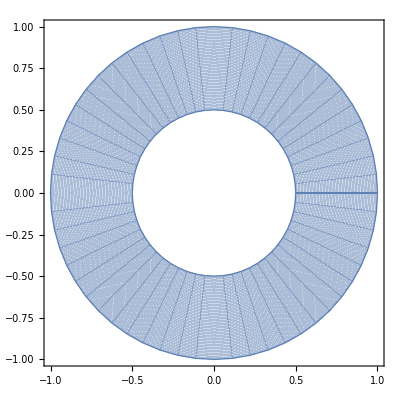

```mathematica
{ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2 Pi}],ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2 Pi},{r,1/2,1}]}
```

```mathematica
ParametricPlot[{r Cos[θ],r Sin[θ]},{θ,0,2 Pi},{r,1/2,1}]
```

-Graphics-

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ], r},{θ,0,2 Pi},{r,1/2,1}]
```

-Graphics3D-

```mathematica
Manipulate[
ParametricPlot3D[{r Cos[θ],r Sin[θ], (1-a)0+a r},{θ,0,2 Pi},{r,1/2,1}, PlotRange->{-1,1}],
{a, 0, 1,.1}]
```

```mathematica
{ContourPlot3D[Sin[x y]==z,{x,-2,2},{y,-2,2},{z,-2,2}],RegionPlot3D[Sin[x y]≥z,{x,-2,2},{y,-2,2},{z,-2,2}]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
$TrigFunctions={Sin,Cos,Sec,Csc,Tan,Cot,ArcSin,ArcCos,ArcSec,ArcCsc,ArcTan,ArcCot,Sinh,Cosh,Sech,Csch,Tanh,Coth,ArcSinh,ArcCosh,ArcSech,ArcCsch,ArcTanh,ArcCoth};
```

```mathematica
Table[Plot3D[Abs[f[x+I y]],{x,-2,2},{y,-2,2},MeshFunctions->Function@@@{{{x,y,z},Re[f[x+I y]]},{{x,y,z},Im[f[x+I y]]}},MeshStyle->{Orange,Green},PlotLabel->f,Ticks->None],{f,$TrigFunctions}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π}]
```

-Graphics3D-

```mathematica
Integers
```

ℤ

```mathematica
RandomInteger[{-100,100}]
```

-13

```mathematica
Reals
```

ℝ

```mathematica
ChampernowneNumber[]
```

ChampernowneNumber[]

```mathematica
RandomReal[{-100,100}]
```

40.7797

```mathematica
Primes
```

Primes

```mathematica
Primes==Integers_(>0)-Primes^C
```

```mathematica
ParametricPlot3D[{Sin[u] Sin[v]+0.05 Cos[20 v],Cos[u] Sin[v]+0.05 Cos[20 u],Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Orange,Specularity[White,10]},Axes->None,Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{u Cos[v],u Sin[v],Im[(u Exp[I v]^5)^(1/5)]},{u,0,2},{v,0,2 Pi},Mesh->None,ExclusionsStyle->{None,Red},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->All,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u],Sqrt[u]+Sin[5 u]/5},{u,0,4 Pi},Mesh->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{v Cos[u],v Sin[u],1/Abs[v Exp[I u]]},{u,0,2 Pi},{v,0,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->False,PlotRange->All]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->False,PlotRange->1]
```

-Graphics3D-

```mathematica
Subscript[𝒟,2]=Rectangle[{0,0},{π,π}];
```

```mathematica
ParametricPlot3D[{2 Cos[u]+Cos[v] Cos[u],2 Sin[u]+Cos[v] Sin[u],Sin[v]},{u,v}∈Subscript[𝒟,2]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,{0,Pi}}]],{u,0,2 Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Evaluate[Table[{(2+Cos[8 u+i]) Cos[u],(2+Cos[8 u+i]) Sin[u],Sin[8 u+i]},{i,{0,Pi}}]],{u,0,2 Pi},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{{4+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]},{8+(3+Cos[v]) Cos[u],3+Sin[v],4+(3+Cos[v]) Sin[u]},{12+(3+Cos[v]) Sin[u],4+(3+Cos[v]) Cos[u],4+Sin[v]}},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
25 20
```

500

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->25,MeshShading->{{Red,Yellow},{Pink,Orange}}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->25,ColorFunction->Function[{x,y,z,u,v},Hue[u/(2 Pi)]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->25,ColorFunction->Function[{x,y,z,u,v},Hue[u/(2 Pi)]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[8 u]) Cos[u],(2+Cos[8 u]) Sin[u],Sin[8 u]},{u,0,2 Pi},PlotStyle->Thick,RegionFunction->Function[{x,y,z,u},Cos[8 u]>-0.25],ColorFunction->Function[{x,y,z,u},Hue[u/(2 Pi)]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2+Cos[v]) Cos[u],(2+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},RegionFunction->Function[{x,y,z,u,v},Sin[8 u] Sin[8 v]>-0.25],Mesh->None,PlotStyle->FaceForm[Red,Cyan],PlotPoints->35,BoundaryStyle->Black]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[u],Cos[v],Sin[u] Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Axes->False]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[ϕ],Cos[ϕ], Tan[ϕ]},{ϕ,0,2π}]
```

-Graphics3D-